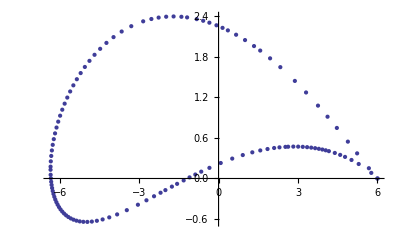

```mathematica
pts  = {{6.0,0},{5.675933771170406,0.1518083785574198},{5.232181944862617,0.3712409078545247},{4.882678099594884,0.5444970141999295},{4.466930525217295,0.7467727490974172},{4.114903979291806,0.9128072826811411},{3.7544435025614336,1.076517491997215},{3.3038109038393184,1.270809179466688},{2.881218352965666,1.4414053067452208},{2.3324909687497715,1.6447194735142516},{1.9453982476097296,1.7750363333334285},{1.5726927010647314,1.8897978985603143},{1.338901345782035,1.9562652332766972},{0.9997343643343399,2.0449331015022874},{0.66219450353495,2.1238452587640286},{0.35158348115975135,2.1880351979403616},{0.15038548828365172,2.2252121609476574},{-0.07874094712520657,2.2632544508678123},{-0.3462101420778596,2.301768660856903},{-0.5803099013000803,2.3301605243237247},{-0.8245416997977937,2.354373333323573},{-1.1874579885392553,2.379875638928914},{-1.4030002020443946,2.3889230698951964},{-1.698223096611894,2.3936914530608178},{-1.9781017219912171,2.389799728779801},{-2.2626800206719255,2.3771057357354026},{-2.536759350001122,2.3561813545293546},{-2.8461816484186646,2.3217669256771396},{-3.2955908096653443,2.249917285468703},{-3.6583968523322548,2.171246757925067},{-3.9658517907946074,2.0884988206630215},{-4.233553192168042,2.00306838631698},{-4.470623312308792,1.9157904906813459},{-4.6829414407310885,1.827219402918161},{-4.874554391569966,1.7377510277680235},{-5.0483825084983565,1.6476845083082734},{-5.206608852185082,1.557256408386248},{-5.350909737864662,1.4666611342973155},{-5.48259911384624,1.3760638751808307},{-5.602723068836078,1.2856092159441195},{-5.712123940307832,1.195427121770988},{-5.811485076866109,1.1056372637760101},{-5.901362825872752,1.0163522667960925},{-5.982209806658275,0.9276802428446138},{-6.054392059944287,0.8397268470354977},{-6.118201770287952,0.7525970165638193},{-6.173866695609237,0.6663965064605212},{-6.22155707168493,0.5812333067710889},{-6.261390513057943,0.4972190080444596},{-6.293435259549403,0.4144701718486283},{-6.3177119913583315,0.33310975836049317},{-6.334194337381129,0.2532686628214576},{-6.342808118254079,0.175087416411551},{-6.344150040235138,0.129038122599692},
{-6.34003241172379,0.05507144604252032},{-6.332225190857292,0.0036334264046591746},{-6.319925790583957,-0.04790464758583492},{-6.304473589111393,-0.09475996500167982},{-6.285045739212425,-0.1405005257270754},{-6.261518584985394,-0.18505569380778938},{-6.233750245446153,-0.22834893052673477},{-6.201578323673754,-0.2702969854941379},{-6.164817131827487,-0.31080894611229853},{-6.123254315573275,-0.34978511217876235},{-6.076646725136111,-0.38711565274967064},{-6.024715330434397,-0.42267898929485603},{-5.96713890857432,-0.45633983115858334},{-5.903546134282829,-0.4879467641611398},{-5.833505563487017,-0.5173292573967738},{-5.756512794727266,-0.5442939014878043},{-5.671973785830416,-0.5686196150097141},{-5.579182833067599,-0.590051440037108},{-5.4772929813620514,-0.6082923680603645},{-5.365275438716557,-0.6229923502052002},{-5.241862566546463,-0.6337331704719329},{-5.105465531959453,-0.6400070432767246},{-4.954051351241599,-0.6411853243246464},{-4.784951807418119,-0.6364709231271948},{-4.594551510805633,-0.6248223123240859},{-4.377745996407429,-0.6048244636937448},{-4.126920669729473,-0.5744512272801174},{-3.829800544686157,-0.5305766767558784},{-3.464116970691644,-0.46779257048072154},{-3.0450298321453513,-0.38761034812596495},{-2.722681716352236,-0.3221238949704266},{-2.4361528383644817,-0.26232425906964574},{-2.189989141525067,-0.2103828338209044},{-2.00714049850417,-0.17173969170097347},{-1.7618652803593355,-0.12013462805672814},{-1.5651483066634977,-0.0791566600252569},{-1.317682378298299,-0.028406151103889332},{-1.0955244730648723,0.01616064388357774},{-0.8773798041928841,0.058801363084177716},{-0.6540972876173851,0.10110706472740993},{-0.3447012845635964,0.15715833391490452},{0.08188486394655695,0.22880342920105878},{0.5161325795773826,0.29404051555647337},{0.9146407410930649,0.34621362717521986},{1.2745633440565811,0.3863762579193568},{1.5751231737794926,0.4144640400488169},{1.848576980495832,0.43544142366630645},{2.098447839170791,0.4505997970124578},{2.300104655033679,0.45991884347948897},{2.5249500286881976,0.4671168810411719},{2.62749,0.469247},{2.822924634816464,0.47124689535393394},{3.0067169792054003,0.47059050891057863},{3.1800736493112587,0.46764239901739746},{3.3439688838502146,0.46270886279568213},{3.499206040664296,0.4560518373632534},{3.6464586861388764,0.4478984702890023},
{3.7863, 0.438448},{3.919222892050784,0.4278769421686186},{4.045658007187435,0.4163427654118612},{4.1659834290077695,0.40398703476436704},{4.389613106059177,0.3773107137817462},{4.5924071301873335,0.3487383320820201},{4.776250888438279,0.3190133493423495},{5.019886117543754,0.27361004424969004},{5.2914147262645725,0.21414032992014786},{5.766762968520808,0.08279757697627987},{6.0,0}};
ListPlot[pts]
```

```mathematica
Table[VectorAngle[pts[[i+2]] - pts[[i]], pts[[i+1]] - pts[[i]]], {i, 1, Length[pts] - 2}]
```

{0.0122722,0.000434073,0.00401373,0.005532,0.00726039,0.0106519,0.0112615,0.0162169,0.0123725,0.0127165,0.00833514,0.0125717,0.0129488,0.0123623,0.0082625,0.00966879,0.0115725,0.0104012,0.0111564,0.017115,0.0104988,0.0149079,0.014626,0.0154709,0.0155278,0.0183599,0.0283654,0.0247075,0.0227956,0.0215654,0.020756,0.0202368,0.019936,0.0198124,0.0198421,0.0200122,0.0203175,0.0207584,0.0213403,0.0220726,0.022969,0.0240473,0.0253291,0.0268401,0.0286095,0.0306686,0.0330489,0.0357775,0.03887,0.0423195,0.0460811,0.0297664,0.0522564,0.0391946,0.0421996,0.0406411,0.0416985,0.0423808,0.0426726,0.0425526,0.0420262,0.0411246,0.0398994,0.0384159,0.0367444,0.0349532,0.0331032,0.0312449,0.0294174,0.0276488,0.0259575,0.0243535,0.0228405,0.0214172,0.020078,0.0188139,0.0176124,0.0164568,0.0153234,0.0141754,0.012946,0.0101678,0.00495626,0.00250661,0.00101823,0.000137062,0.000517177,0.000889779,0.00172448,0.00203103,0.00244865,0.00292405,0.00466245,0.00742528,0.00870601,0.00904828,0.00903109,0.00815841,0.00791084,0.00762183,0.00643335,0.00747205,0.00351716,0.00691116,0.00668997,0.00652074,0.00636155,0.00621034,0.00606588,0.00592723,0.00579357,0.00566438,0.0055391,0.0106694,0.0101183,0.00968074,0.0136718,0.0165837,0.0345164,0.0238992}

```mathematica
perp = Table[Cross[pts[[i+1]] - pts[[i]]], {i,1,Length[pts]-1}];
h1= Table[y/.Solve[pts[[i]][[2]]+y*perp[[i]][[2]] == 10, y],  {i,1,Length[pts]-1}];
h2= Table[y/.Solve[pts[[i]][[1]]+y*perp[[i]][[1]] == -10, y],  {i,1,Length[pts]-1}];
h3 = Table[y/.Solve[pts[[i]][[2]]+y*perp[[i]][[2]] == -10, y],  {i,1,Length[pts]-1}];
h4= Table[y/.Solve[pts[[i]][[1]]+y*perp[[i]][[1]] == 10, y],  {i,1,Length[pts]-1}];
Table[pts[[i]] [[1]]+ h1[[i]]  perp[[i]][[1]], {i,1,Length[pts]-1}]
Table[pts[[i]] [[2]]+ h2[[i]]  perp[[i]][[2]], {i,1,Length[pts]-1}]
Table[pts[[i]] [[1]]+ h3[[i]]  perp[[i]][[1]], {i,1,Length[pts]-1}]
Table[pts[[i]] [[2]]+ h4[[i]]  perp[[i]][[2]], {i,1,Length[pts]-1}]
```

{{10.6845},{10.5458},{10.0054},{9.48311},{8.83125},{8.24203},{7.60183},{6.82769},{6.05234},{5.14534},{4.47799},{3.87844},{3.44176},{2.85952},{2.28986},{1.79506},{1.44125},{1.03531},{0.587439},{0.180068},{-0.28728},{-0.867602},{-1.28007},{-1.80399},{-2.31756},{-2.84464},{-3.38692},{-4.07375},{-4.97611},{-5.76542},{-6.49062},{-7.17764},{-7.84305},{-8.499},{-9.15552},{-9.82182},{-10.5071},{-11.2215},{-11.9765},{-12.7862},{-13.6686},{-14.6472},{-15.7545},{-17.0367},{-18.5624},{-20.4384},{-22.8414},{-26.0871},{-30.8003},{-38.4181},{-53.1445},{-94.7984},{-343.494},{170.972},{59.1823},{35.5555},{24.1481},{17.4624},{12.9188},{9.61786},{7.1027},{5.1166},{3.5043},{2.16645},{1.03659},{0.0686843},{-0.77012},{-1.50378},{-2.15009},{-2.72244},{-3.23095},{-3.68329},{-4.08517},{-4.44074},{-4.75274},{-5.02267},{-5.25072},{-5.43569},{-5.57457},{-5.66192},{-5.68841},{-5.63779},{-5.46688},{-5.15532},{-4.87695},{-4.60154},{-4.34785},{-4.14724},{-3.86998},{-3.63219},{-3.32947},{-3.04706},{-2.76095},{-2.44742},{-1.99781},{-1.38604},{-0.754582},{-0.162595},{0.376155},{0.839791},{1.26834},{1.65715},{1.9947},{2.39282},{2.85696},{3.16877},{3.46701},{3.75296},{4.02765},{4.34761},{4.79245},{5.02976},{5.31067},{5.74539},{6.15288},{6.58038},{7.15014},{7.99533},{9.2873}}

{{-34.1553},{-31.5492},{-30.3561},{-30.0446},{-29.926},{-30.1657},{-30.825},{-31.6848},{-33.3239},{-34.9877},{-37.0195},{-38.8158},{-41.4166},{-45.0055},{-49.4698},{-53.8337},{-58.91},{-66.6368},{-77.2967},{-92.6852},{-128.219},{-207.566},{-529.873},{599.427},{182.227},{103.725},{69.4586},{47.0679},{33.1687},{25.7339},{20.9969},{17.6663},{15.1705},{13.2147},{11.6298},{10.3118},{9.19221},{8.22444},{7.37518},{6.61999},{5.94038},{5.32196},{4.7533},{4.22503},{3.7293},{3.25931},{2.80899},{2.37269},{1.94501},{1.52045},{1.09328},{0.657156},{0.281662},{-0.0744783},{-0.500435},{-0.87167},{-1.26154},{-1.6644},{-2.10217},{-2.58292},{-3.11686},{-3.71704},{-4.40051},{-5.18994},{-6.1162},{-7.22235},{-8.57041},{-10.2529},{-12.414},{-15.2917},{-19.3072},{-25.2838},{-35.0725},{-53.8763},{-104.078},{-629.609},{180.351},{84.6052},{57.978},{45.8243},{39.1983},{35.4075},{33.6932},{33.8473},{34.547},{35.5847},{36.7444},{37.8178},{39.4275},{41.0503},{43.2515},{45.5704},{48.2065},{51.6893},{57.6463},{67.3384},{80.6183},{98.1592},{121.032},{151.304},{195.748},{262.251},{384.679},{904.124},{-3590.03},{-764.359},{-437.383},{-310.709},{-243.344},{-185.465},{-152.152},{-136.366},{-118.351},{-101.754},{-89.9027},{-78.9707},{-68.3046},{-55.1277},{-44.3315}}

{{1.31551},{0.655927},{0.0909486},{-0.247588},{-0.601822},{-0.841362},{-1.02123},{-1.2461},{-1.35804},{-1.58777},{-1.68031},{-1.8076},{-1.78681},{-1.8162},{-1.84328},{-1.9005},{-1.87939},{-1.84459},{-1.83818},{-1.80271},{-1.69269},{-1.70711},{-1.6031},{-1.52589},{-1.42544},{-1.31776},{-1.16249},{-0.87623},{-0.63933},{-0.382647},{-0.108099},{0.185403},{0.500194},{0.839452},{1.20719},{1.6084},{2.04929},{2.53772},{3.0837},{3.70031},{4.40487},{5.22091},{6.18124},{7.33307},{8.74686},{10.5328},{12.8737},{16.0957},{20.8455},{28.6094},{43.7363},{86.7275},{342.825},{-188.296},{-72.5881},{-48.2504},{-36.4974},{-29.6252},{-24.9567},{-21.5639},{-18.9747},{-16.924},{-15.251},{-13.8526},{-12.6597},{-11.6239},{-10.7105},{-9.89392},{-9.15456},{-8.47735},{-7.85033},{-7.26381},{-6.70976},{-6.18137},{-5.67268},{-5.1783},{-4.69313},{-4.2121},{-3.7298},{-3.24005},{-2.73509},{-2.204},{-1.64036},{-1.09223},{-0.702873},{-0.381468},{-0.121056},{0.0606917},{0.296202},{0.469426},{0.682705},{0.862334},{1.02848},{1.17585},{1.36119},{1.61856},{1.86384},{2.06914},{2.24519},{2.37404},{2.48164},{2.5814},{2.63496},{2.67003},{2.78553},{2.82865},{2.86498},{2.8953},{2.92026},{2.87956},{2.96793},{2.97605},{2.92491},{2.92752},{2.91916},{2.85322},{2.76978},{2.46916},{2.18744}}

{{8.53882},{8.89624},{9.9892},{11.0624},{12.478},{13.8707},{15.5622},{17.8583},{20.6544},{24.4203},{27.9336},{31.5319},{35.0862},{40.5428},{47.3089},{54.4043},{61.5489},{72.257},{87.6095},{109.053},{156.395},{268.905},{708.378},{-838.9},{-266.139},{-158.246},{-110.363},{-78.0293},{-59.0656},{-48.5773},{-41.6743},{-36.6591},{-32.7725},{-29.619},{-26.9701},{-24.6832},{-22.664},{-20.8469},{-19.1849},{-17.6422},{-16.1916},{-14.8108},{-13.4818},{-12.1887},{-10.9177},{-9.65591},{-8.39078},{-7.10984},{-5.80006},{-4.44725},{-3.03551},{-1.54639},{-0.301158},{1.0389},{2.53515},{3.90127},{5.33417},{6.8304},{8.45874},{10.2451},{12.2221},{14.4313},{16.9268},{19.7803},{23.0888},{26.9874},{31.6694},{37.4222},{44.6924},{54.2142},{67.2846},{86.4319},{117.333},{175.925},{330.732},{1940.48},{-537.024},{-242.301},{-158.851},{-119.338},{-96.2425},{-81.0817},{-70.8405},{-64.6},{-61.2826},{-59.2004},{-57.89},{-57.2408},{-56.5836},{-56.4723},{-56.4451},{-56.7472},{-57.3502},{-58.7082},{-61.4368},{-65.7907},{-72.1455},{-81.0734},{-92.9822},{-109.409},{-133.933},{-170.533},{-240.062},{-538.847},{2010.1},{411.694},{227.03},{155.677},{117.863},{87.0057},{67.084},{58.4023},{49.311},{40.1973},{33.7937},{28.3498},{23.012},{17.2552},{12.0076}}